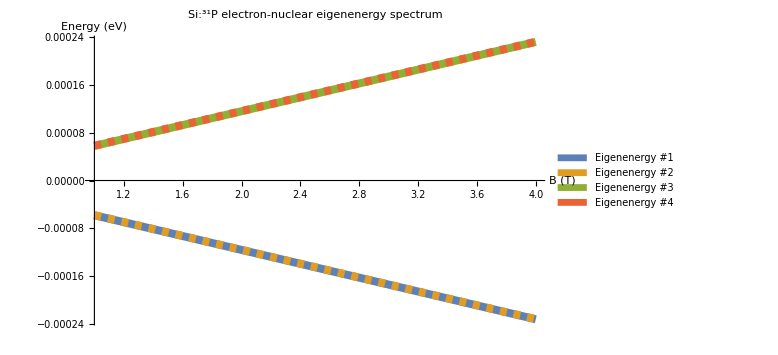

```mathematica
(* Define constants *)
e = 1.602*10^-19; (* Charge of electron [C] *)
h = 4.136*10^-15; (* Planck constant [eVs] *)
ℏ= 6.582*10^-16; (* Reduced Planck constant [eVs] *) 
me =9.109*10^-31; (* Mass of electron [kg] *)
mn =30.973*1.661*10^-27; (* Mass of phosphorous 31 [kg] *)
A=(58*10^6/2)*h;  (* Contact hyperfine energy [eV] *)
g=1.13; (* Nuclear g-factor [unitless] *)

(* Calculate Bohr magneton (ub) and nuclear magneton (un) *)
μb = (e*ℏ)/(2*me);
μn=(e*ℏ)/(2*mn);

(* Define Pauli matrices, identity matrix, and Kronecker product *)
X = PauliMatrix[1];
Y = PauliMatrix[2];
Z = PauliMatrix[3];
IM=IdentityMatrix;
KP=KroneckerProduct;

(* Define Hamiltonian and calculate eigenenergies and eigenstates *)
{vals, vects}=Eigensystem[m=μb*B KP[X,IM[2]] - g*μn*B KP[IM[2],X] + A (KP[X,X]+KP[Y,Y]+KP[Z,Z])];

(* Plot eigenenergies *)
Plot[{vals[[1]],vals[[2]],vals[[3]],vals[[4]]},{B,1,4},
PlotStyle->{Directive[Thickness[0.01]],Directive[Dashed,Thickness[0.01]],Directive[Thickness[0.01]],Directive[Dashed,Thickness[0.01]]},
PlotLegends->{SwatchLegend[{"Eigenenergy #1","Eigenenergy #2", "Eigenenergy #3","Eigenenergy #4"},LegendMarkerSize->30]}, AxesLabel->{Style["B (T)",16],Style["Energy (eV)",16]},
PlotLabel->Style["Si:^31P electron-nuclear eigenenergy spectrum", Black, FontSize->20], ImageSize->Large]
```